# FibonacciEncode

FibonacciEncode[n]
gives the Fibonacci-digit encoding for the number n.

Fibonacci encoding is made unique by allowing no pair of 1s to appear together.

## See AlsoSeeAlsoInsert links to any related reference (function) pages.

Fibonacci ▪ IntegerDigits ▪ NumberExpand ▪ NumberDecompose ▪ InverseFibonacci ▪ HuffmanEncode ▪ ZeckendorfRepresentation ▪

## Tech NotesTechNotesInsert links to related tech notes.

## Related Guides

## Related LinksRelatedLinksInsert links to any related page, including web pages.

A New Kind of Science, §10 .5 Notes: Number Representations

## Examples InitializationExamplesInitializationInput that is to be evaluated before any examples are run, e.g. Needs[…].

```mathematica
Needs["PeterBurbery`CombinatoricsPaclet`"]
```

## Basic Examples | More Examples ⊳

Fibonacci encoding for 42:

```mathematica
FibonacciEncode[42]
```

{1,0,0,1,0,0,0,0}

## More ExamplesMoreExamplesExtended examples in standardized sections.

### Scope

The Fibonacci encoding of a large integer, a googol:

```mathematica
FibonacciEncode[10^100]
```

{1,0,0,0,0,0,1,0,1,0,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,1,0,0,1,0,1,0,1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,1,0,1,0,0,0,1,0,1,0,0,1,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,1,0,0,0,0,1,0,1,0,0,1,0,0,0,0,1,0,1,0,1,0,1,0,0,1,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,1,0,1,0,1,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,1,0,0,1,0,0,1,0,1,0,0,1,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,1,0,1,0,1,0,1,0,0,1,0,0,1,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,0,1,0,0}

### Generalizations & Extensions

### Options

### Applications

### Properties & Relations

Get the Fibonacci encoding for a random integer:

```mathematica
n=RandomInteger[10000]
```

5057

```mathematica
enc=FibonacciEncode[n]
```

{1,0,0,0,1,0,1,0,0,0,0,1,0,1,0,1,0,1}

Decode the encoding to retrieve the original integer:

```mathematica
Total[MapIndexed[Fibonacci[#2[[1]]+1]*#1&,Reverse[enc]]]
```

5057

### Possible Issues

### Interactive Examples

### Neat Examples

Visualize the Fibonacci encoding for the first 30 integers:

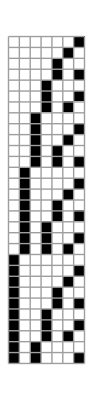

```mathematica
ArrayPlot[PadLeft[Table[FibonacciEncode[n],{n,30}]],Mesh->True]
```

## Metadata

### CategorizationMetadataMetadata such as page URI, context, and type of documentation page.

Symbol

PeterBurbery/CombinatoricsPaclet

PeterBurbery`CombinatoricsPaclet`

PeterBurbery/CombinatoricsPaclet/ref/FibonacciEncode

### Keywords

### Syntax Templates